```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];

Solve[Cos[θ1]*Exp[-λ Sin[θ1]^2]==Cos[θ2]*Exp[-μ Sin[θ2]^2],θ2]
```

Solve[ⅇ^(-λ Sin[θ1]^2) Cos[θ1]==ⅇ^(-μ Sin[θ2]^2) Cos[θ2],θ2]

```mathematica
Assuming[{0≤k1≤1&&0≤k2≤1&&5≤λ&&5≤μ},
Simplify[Solve[k1*Exp[-λ (1-k1^2)]==k2*Exp[-μ (1-k2^2)],μ]]
]
```

{{μ→ConditionalExpression[(-λ+k1^2 λ+2 ⅈ π C[1]+Log[k1]-Log[k2])/(-1+k2^2),C[1]∈ℤ]}}

```mathematica
Simplify[ProductLog[2 ⅇ^(2 (-1+k1) (1+k1) λ+2 μ) k1^2 μ],]
```

ProductLog[2 ⅇ^(2 ((-1+k1^2) λ+μ)) k1^2 μ]

```mathematica
asgPolar[0,π/2,π/2,λ,μ,1]
asgPolar[θ,π/2-θ,π/2,λ,μ,1]
asgPolar[θ,π/2,π/2-θ,λ,μ,1]
```

1

ⅇ^(-λ Sin[θ]^2) Cos[θ]

ⅇ^(-μ Sin[θ]^2) Cos[θ]

```mathematica
asgPolar[θ,π/2-θ,π/2,λ,μ,1]/.{θ->ArcTan[s1]}
(*Solve[ⅇ^(-s1^2 λ) √(1-s1^2)==0.1,λ]//FullSimplify*)
Solve[(ⅇ^(-(s1^2 λ)/(1+s1^2)))/(√(1+s1^2))==0.1,λ]//FullSimplify
asgPolar[θ,π/2,π/2-θ,λ,μ,1]/.{θ->ArcTan[k*s1]}
(*Solve[ⅇ^(-k^2 s1^2 μ) √(1-k^2 s1^2)==0.1,μ]//FullSimplify*)
Solve[(ⅇ^(-(k^2 s1^2 μ)/(1+k^2 s1^2)))/(√(1+k^2 s1^2))==0.1,μ]//FullSimplify
```

(ⅇ^(-(s1^2 λ)/(1+s1^2)))/(√(1+s1^2))

{{λ→-(0.5 (1.+1. s1^2) (-4.60517+Log[1.+s1^2]))/s1^2}}

(ⅇ^(-(k^2 s1^2 μ)/(1+k^2 s1^2)))/(√(1+k^2 s1^2))

{{μ→-(0.5 (1.+1. k^2 s1^2) (-4.60517+Log[1.+k^2 s1^2]))/(k^2 s1^2)}}

```mathematica
λ1=-(0.5(1+ s1^2) (2Log[0.1]+Log[1+s1^2]))/s1^2;
μ1=-(0.5 (1+ k^2 s1^2) (2Log[0.1]+Log[1+k^2 s1^2]))/(k^2 s1^2);
λ1/μ1
```

(1. k^2 (1+s1^2) (-4.60517+Log[1+s1^2]))/((1+k^2 s1^2) (-4.60517+Log[1+k^2 s1^2]))

```mathematica
Log[0.1]
```

-2.30259

```mathematica
Series[ Log[1+k^2 s1^2],{k,1,1}]
Series[Log[1+x],{x,0,2}]
```

Log[1+s1^2]+(2 s1^2 (k-1))/(1+s1^2)+O[k-1]^2

x-x^2/2+O[x]^3

```mathematica
(1. k^2 (1+s1^2) (-4.605170185988091+Log[1+s1^2]))/((1+k^2 s1^2) (-4.605170185988091+Log[1+k^2 s1^2]))//FullSimplify
```

(1. k^2 (1+s1^2) (-4.60517+Log[1+s1^2]))/((1+k^2 s1^2) (-4.60517+Log[1+k^2 s1^2]))

```mathematica
Log[2]//N
```

0.693147

```mathematica
(k^2 (2.3025850929940455))/(2.3025850929940455+0.5 ((2 (-1+k) s1^2)/(-1+s1^2)))//FullSimplify
```

(2.30259 k^2 (-1.+s1^2))/(-2.30259+(1.30259+1. k) s1^2)

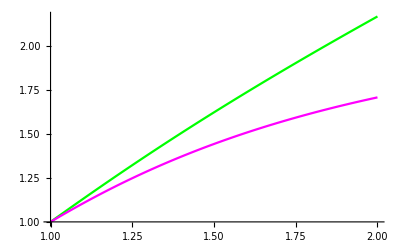

```mathematica
p1=Plot[{(1. k^2 (1+s1^2) (-4.605170185988091+Log[1+s1^2]))/((1+k^2 s1^2) (-4.605170185988091+Log[1+k^2 s1^2]))}/.{s1->0.9},{k,1,2},PlotStyle->{Green}];
p2=Plot[((k^2 (1+s1^2))/(1+k^2 s1^2))/.{s1->0.9},{k,1,2},PlotStyle->{Magenta}];
Show[p1,p2]
```

```mathematica
Quiet@FindMinimum[NIntegrate[Abs[-(0.5 (1+ s1^2) (-4.6+Log[1+s1^2]))/s1^2-a/(b+c*s1)],{s1,0.1},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],{a,1},{b,2},{c,1}];

Quiet@FindMinimum[NIntegrate[Abs[GGX[m,θ]-ApproxNew1[0.5,θ,a,b,c]],{m,0.0001,1},{θ,-π/2,π/2},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],{a,1/π},{b,2},{c,1}]
```

FindMinimum[NIntegrate[Abs[-(0.5 (1.+1. s1^2) (-4.60517+Log[1+s1^2]))/s1^2-a/(b+c s1)],{s1,0.1},PrecisionGoal→1,AccuracyGoal→1,Method→QuasiMonteCarlo,MaxRecursion→2],{a,1},{b,2},{c,1}]

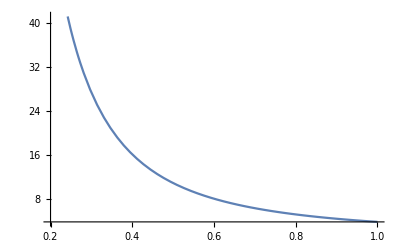

```mathematica
Plot[-(0.5 (1.+1. s1^2) (-4.605170185988091+Log[1+s1^2]))/s1^2,{s1,0.2,1}]
```

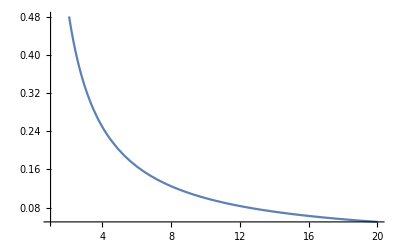

```mathematica
Plot[1/x,{x,1,20}]
```